{{x→4}}{{y→2}}

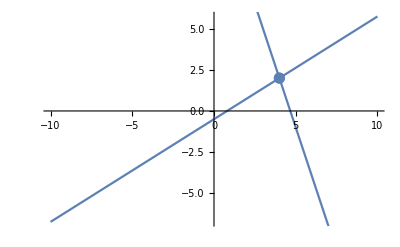

```mathematica
sustitucion[ec1_,ec2_]:=Block[{ec1Desp,despejada,valueY,valueX,r,img1,img2},
ec1Desp = Solve[ec1, x];
     despejada = ec2/.x -> ec1Desp[[1,1,2]];
     valueY = Solve[despejada];
     r= ec1 /.y-> valueY[[1,1,2]];
     valueX = Solve[r];
     Print[valueX, valueY];
     img1=Plot[Solve[ec1,y][[1,1,2]],{x,-10,10}];
     img2=Plot[Solve[ec2,y][[1,1,2]],{x,-10,10}];
     Show[img1,img2, ListPlot[{{valueX[[1,1,2]], valueY[[1,1,2]]}}, PlotStyle->PointSize[0.02]]]
    

]
sustitucion[-5 x+8 y+4==0,3 x+y-8==6]
```

```mathematica
igualacion[n1_,n2_]:=Block[{ecDn1,ecDn2,s1,s2,res,valueY,valueX},
     ecDn1 = Solve[n1, x];
     ecDn2 = Solve[n2, x];
     s1 = ToString[ecDn1[[1,1,2]],InputForm];
     s2 = ToString[ecDn2[[1,1,2]],InputForm];
     res=s1<>"=="<>s2;
     valueY=Solve[ToExpression[res]];
     valueX=ecDn1/.y->valueY[[1,1,2]];
     Print[valueX,valueY];
     img1=Plot[Solve[n1,y][[1,1,2]],{x,-10,10}];
     img2=Plot[Solve[n2,y][[1,1,2]],{x,-10,10}];
     Show[img1,img2, ListPlot[{{valueX[[1,1,2]], valueY[[1,1,2]]}}, PlotStyle->PointSize[0.02]]]

]
igualacion[-5 x+8 y+4==0,3 x+y-8==6]
```

{{x→4}}{{y→2}}

-Graphics-

```mathematica
reduccion[e1_,e2_]:=Block[{exp,exp2,coef1,coef2,ec2,ec1,sum,valueY,valueX,img1,img2},
     exp=e1[[1]];
     exp2=e2[[1]];
     coef1=D[exp,x];
     coef2=D[exp2,x]*-1;
     ec1=Expand[ exp*coef2];
     ec2=Expand[ exp2*coef1];
     sum=ToString[Expand[ec1+ec2],InputForm]<>"==0";
     valueY=Solve[ToExpression[sum],y];
     valueX=Solve[e1 /.y-> valueY[[1,1,2]],x];
     Print[valueX,valueY];
     img1=Plot[Solve[e1,y][[1,1,2]],{x,-10,10}];
     img2=Plot[Solve[e2,y][[1,1,2]],{x,-10,10}];
     Show[img1,img2, ListPlot[{{valueX[[1,1,2]], valueY[[1,1,2]]}}, PlotStyle->PointSize[0.02]]]
 ]    
reduccion[-5 x+8 y+4==0,3 x+y-14==0]
```

{{x→4}}{{y→2}}

-Graphics-

```mathematica
determinantes[e1_,e2_]:=Block[{b1,b2,a1,a2,a3,a4,cram,valueY,valueX,img1,img2},
     a1=D[e1[[1]],x];
     a2=D[e2[[1]],x];
     a3=D[e1[[1]],y];
     a4=D[e2[[1]],y];
     b1=e1[[2]];
     b2=e2[[2]];
     cram= a1*a4-a2*a3;
     valueY=(a1*b2-a2*b1)/cram;
     valueX=(b1*a4-b2*a3)/cram;
     Print["X -> " ,valueX];
     Print["Y -> " ,valueY];
     img1=Plot[Solve[e1,y][[1,1,2]],{x,-10,10}];
     img2=Plot[Solve[e2,y][[1,1,2]],{x,-10,10}];
     Show[img1,img2, ListPlot[{{valueX, valueY}}, PlotStyle->PointSize[0.02]]]
]
determinantes[-5 x+8 y==-4,3 x+y==14]
```

X -> 4

Y -> 2

-Graphics-